# Kane-Mele Static

## Bulk

### Import

```mathematica
(*仅修改当前笔记本的Input单元样式*)SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Input"],CellFrame->{{2,0},{0,0}},Background->LightBlue]}]]
```

```mathematica
LaunchKernels[10(*8*)];
Needs["TBMethod`"]
ParallelNeeds["TBMethod`"]
StringTemplate["TBMethod<*\"`\"*>`1`<*\"`\"*>*"] /@ {"MDConstruct","EigenSpect", "LGFF", "DataVisualization"};
Scan[Echo@*Information][%]
```

### Lattice

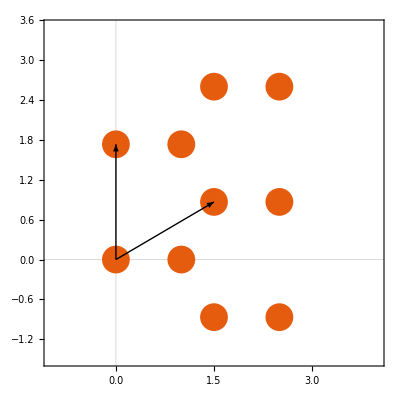

```mathematica
Clear[a,unicell,vasbasis,vas,pts,pts0,pts1,basisArrows]
a=Sqrt[3];(*A-A distance*)
unicell={{0,0},{1,0}};(*元胞*)
vasbasis={{3/2,Sqrt[3]/2},{0,Sqrt[3]}};(*2个基矢*)
vas={{0,0},{1,0},{0,1},{1,1},{1,-1}}.vasbasis;(*由基矢写出平移矢量*)

pts=Module[{pts0=Thread[-1{1,-1}->unicell]},<|#->MapAt[TranslationTransform[#],pts0,{All,2}]&/@vas|>];(*打标签并平移得到整体晶格*)

pts0=Flatten[Values@pts,1];pts1=Flatten[Values@Values@pts,1];(*给出不同数据格式的坐标数据*)
basisArrows=Graphics[{Arrowheads[0.02],Arrow[{{0,0},vasbasis[[1]]}],(*第一基矢*)Arrow[{{0,0},vasbasis[[2]]}]  (*第二基矢*)}];(*绘制基矢-Optional*)
(*绘制图像，并将基矢添加到图像中*)
Show[ListPlot[pts1,PlotRange->{{-1,4},{-1.5,3.5}},AspectRatio->1,PlotStyle->PointSize[0.05]],basisArrows]
```

### tFunc

```mathematica
Clear[tFunckm]
tFunckm[t_,λSO_,λR_,λv_][inf_->ptf_,ini_->pti_]:=Module[{vd=ptf-pti,d,x,y,fills,conds,zero=1.*^-5,theta},d=Norm[vd];{x,y}=Flatten[TakeDrop[vd,1],1];
	conds={
d<zero,
d> zero &&Abs[d]<1.01,
d>zero&&Abs[d]>Sqrt[3]-0.01&&Abs[d]<Sqrt[3]+0.01};
	fills={
Hold[ini*λv*PauliMatrix[0]],
Hold[{-t,ⅈ*λR*y,-ⅈ*λR*x}.PauliMatrix[{0,1,2}]],
Hold[theta=ArcTan@@{x,y};ⅈ*λSO*PauliMatrix[3]*ini*(-1)^Quotient[theta,π/3]]};
	FillWithCondition[fills,conds]];
```

### Willson Loop

```mathematica
Clear[loopfbz]
vbsbasis=ReciprocalVectors[vasbasis];
fig1=FirstBrillouinZonePlot[vbsbasis];
r1=vasbasis[[1]];
r2=vasbasis[[2]];
loopfbz=Module[{Γ,X,Y,Z,n=500},
{Γ,X,Y,Z}={{0,0},{2/3,1/3},{0.5,0.5},{1/3,2/3}(*,{0,0.5}*)}.Take[vbsbasis,2,2]//N;
PathSample[{Γ,X,Y,Z,Γ},n]
];
fig2=ListPlot[loopfbz[[1]],AspectRatio->Automatic,PlotMarkers->"○"];
Show[fig1,fig2]
```

-Graphics-

### Hamiltonian

```mathematica
Clear[params]
params={t->1,λSO->0.06,λR->0.05,λv->0.1,dup->Sqrt[3]+0.01};
```

```mathematica
Print[Style[Row[{"t=",t/.params,",λSO=",λSO/.params,",λR=",λR/.params,",λv=",λv/.params}],FontSize->16]]
(hkm=ParallelHMatrixFromHoppings[{pts[[1]],#},tFunckm[t,λSO,λR,λv]/.params,dup/.params]&/@pts)//AbsoluteTiming
hBloch2D[{kx_,ky_}]:=HBloch[{kx,ky},hkm];
```

t=1,λSO=0.06,λR=0.05,λv=0.1

{0.074505,<|{0,0}→SparseArray[…],{3/2,(√3)/2}→SparseArray[…],{0,√3}→SparseArray[…],{3/2,(3 √3)/2}→SparseArray[…],{3/2,-(√3)/2}→SparseArray[…]|>}

### Plot(Quick Check)

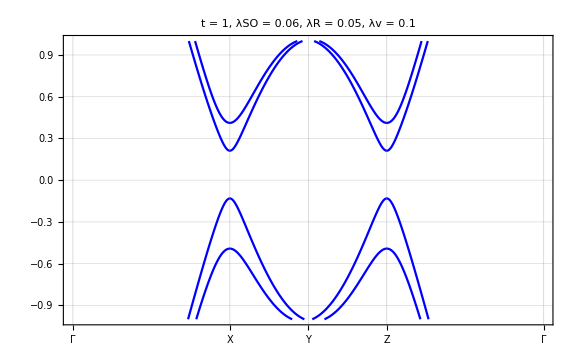
-Graphics-Kane-Mele Model

```mathematica
Clear[banddata]
params={t->1,λSO->0.06,λR->0.05,λv->0.1,dup->Sqrt[3]+0.01};
(hkm=ParallelHMatrixFromHoppings[{pts[[1]],#},tFunckm[t,λSO,λR,λv]/.params,dup/.params]&/@pts)//AbsoluteTiming;
hBloch2D[{kx_,ky_}]:=HBloch[{kx,ky},hkm];
banddata=ParallelBandData[hBloch2D,loopfbz[[1]],Method->"Direct"];
Labeled[BandPlot[banddata,{"Γ","X","Y","Z","Γ"},loopfbz[[2]],PlotRange->{-1,1},AspectRatio->1/GoldenRatio,PlotLabel->Style[Row[{"t = ",t/.params,", λSO = ",λSO/.params,", λR = ",λR/.params,", λv = ",λv/.params}],15,FontFamily->"Times New Roman",Italic],ImageSize->Large],Style["Kane-Mele Model",15,FontFamily->"Times New Roman",Italic],Bottom]
```

## Zigzag Edge

### a. Lattice

```mathematica
crystStruct1Dy[n_]:=Module[{basis0,atombasis,vRs={{0,0},{0,1},{0,-1}},centerize=TranslationTransform[-Mean[#]][#]&},basis0=Thread[-1{-1,1,-1,1}->{{0,0},{1/2,Sqrt[3]/2},{3/2,Sqrt[3]/2},{2,0}}];
atombasis=Join@@CrystalStructure[vasbasisedge,basis0,Tuples[{Range[-n,n],{0}}]];
CrystalStructure[vasbasis,Nest[Delete[{{-1},{-4}}],atombasis,1 0],vRs]]
```

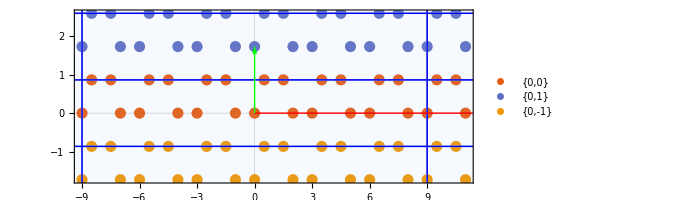

```mathematica
n=3;
vasbasisedge={{3,0},{0,√3}};
CrystalStructurePlot[{2 n,1} vasbasisedge,crystStruct1Dy[n],AspectRatio->Automatic,PlotStyle->PointSize[0.02],PlotRange->All,PlotRangePadding->{Scaled[.1],Scaled[.1]},ImageSize->Full](*For check use*)
```

```mathematica
Clear[cryststruct1dy,n]
n=(*50*)20(*4*);
cryststruct1dy=crystStruct1Dy[n];
```

### b. Hamiltonian

```mathematica
(*计算哈密顿量和hbloch*)
Clear[t,t2,λSO,λv,λR,dup]
(*params2={t->1,λSO->0.06,λR->0.05,λv->0.4,dup->Sqrt[3]+0.01};*)
hkmedge=ParallelHMatrixFromHoppings[{cryststruct1dy[[1]],#},tFunckm[t,λSO,λR,λv]/.params,dup/. params]&/@cryststruct1dy
hBloch1Dy[ky_]:=HBlochFull[{0,ky},hkmedge]
(*!这里注意"hBloch1Dy[ky_] := HBlochFull[{0, ky}, h01km]"中是"HBlochFull"而不是"HBloch"
！当晶格周围被完全包围之后使用HBlochFull
！当晶格周围没有被完全包围使用HBloch，会自动补全。*)
```

<|{0,0}→SparseArray[…],{0,√3}→SparseArray[…],{0,-√3}→SparseArray[…]|>

### e. Plot(Quick Check)

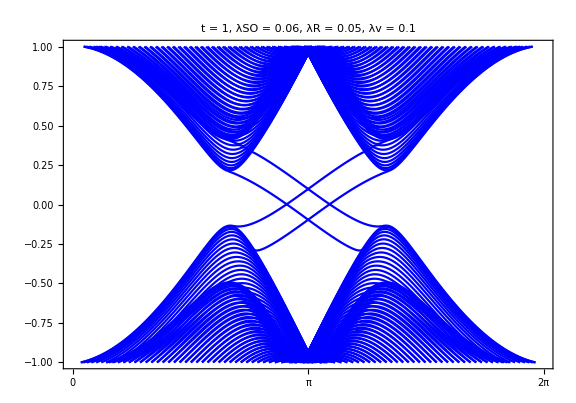

```mathematica
Clear[t,t2,λSO,λv,λR,dup]
params2={t->1,λSO->0.06,λR->0.05,λv->0.1,dup->Sqrt[3]+0.01};
hkmedge=ParallelHMatrixFromHoppings[{cryststruct1dy[[1]],#},tFunckm[t,λSO,λR,λv]/.params2,dup/. params2]&/@cryststruct1dy;
eup = 0.25 4; kn = 200 4; kgrid =  Subdivide[##, kn] & @@ ({-2, 0} π/√3);
hBloch1Dy[ky_]:=HBlochFull[{0,ky},hkmedge]
(banddata1dy = 
    ParallelBandData[hBloch1Dy, kgrid, 
     Method ->(*"Direct"*)"Banded"];) // AbsoluteTiming;
BandPlot[Select[AnyTrue[Between[{-1, 1} eup]]][banddata1dy], {"0", "π", "2π"},  Insert[MinMax[kgrid], Mean[kgrid], 2], DataRange -> MinMax[kgrid], AspectRatio ->0.7, PlotRange ->{-1, 1} eup,PlotStyle -> Directive[Blue],ImageSize->Large,PlotLabel->Style[Row[{"t = ",t/.params2,", λSO = ",λSO/.params2,", λR = ",λR/.params2,", λv = ",λv/.params2}],22,FontFamily->"Times New Roman",Italic]]
```

## Armchair Edge(Not Required)

### a. Lattice

```mathematica
crystStruct1Dx[n_]:=Module[{basis0,atombasis,vRs={{0,0},{2,-1},{-2,1}},centerize=TranslationTransform[-Mean[#]][#]&},basis0=Thread[-1{-1,1,-1,1}->{{-1,0},{1/2-1,Sqrt[3]/2},{3/2-1,Sqrt[3]/2},{2-1,0}}];
atombasis=Join@@CrystalStructure[vasbasisedge,basis0,Tuples[{Range[-n,n],{0}}]];
CrystalStructure[vasbasis,Nest[Delete[{{-1},{-4}}],atombasis,1 0],vRs]]
```

```mathematica
n=3;
(*vasbasisedge={{3,0},{0,√3}};*)
vasbasisedge={{0,√3},{3,0}};
CrystalStructurePlot[{2 n,1} vasbasisedge,crystStruct1Dx[n],AspectRatio->Automatic,PlotStyle->PointSize[0.02],PlotRange->All,PlotRangePadding->{Scaled[.1],Scaled[.1]},ImageSize->Full](*For check use*)
```

```mathematica
Clear[cryststruct1dx,n]
n=(*50*)20(*4*);
cryststruct1dx=crystStruct1Dx[n];
```

### b. Hamiltonian

```mathematica
(*计算哈密顿量和hbloch*)
Clear[t,t2,λSO,λv,λR,dup]
(*params2={t->1,λSO->0.06,λR->0.05,λv->0.4,dup->Sqrt[3]+0.01};*)
hkmedge=ParallelHMatrixFromHoppings[{cryststruct1dx[[1]],#},tFunckm[t,λSO,λR,λv]/.params,dup/. params]&/@cryststruct1dx
hBloch1Dy[ky_]:=HBlochFull[{0,ky},hkmedge]
(*!这里注意"hBloch1Dy[ky_] := HBlochFull[{0, ky}, h01km]"中是"HBlochFull"而不是"HBloch"
！当晶格周围被完全包围之后使用HBlochFull
！当晶格周围没有被完全包围使用HBloch，会自动补全。*)
```

### e. Plot(Quick Check)

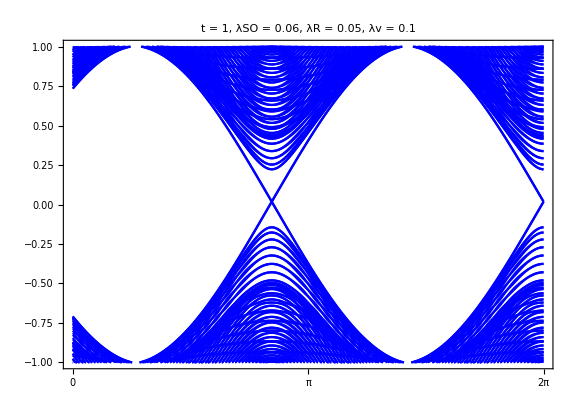

```mathematica
Clear[t,t2,λSO,λv,λR,dup]
kgrid =  Subdivide[##, kn] & @@ ({-2, 0} π/√3);
kgrid=kgrid+0.75;(*注意这里⚠️*)
params2={t->1,λSO->0.06,λR->0.05,λv->0.1,dup->Sqrt[3]+0.01};
hkmedge=ParallelHMatrixFromHoppings[{cryststruct1dx[[1]],#},tFunckm[t,λSO,λR,λv]/.params2,dup/. params2]&/@cryststruct1dx;
hBloch1Dy[kx_]:=HBlochFull[{kx,0},hkmedge]
(banddata1dy = 
    ParallelBandData[hBloch1Dy, kgrid, 
     Method ->(*"Direct"*)"Banded"];) // AbsoluteTiming;
BandPlot[Select[AnyTrue[Between[{-1, 1} eup]]][banddata1dy], {"0", "π", "2π"},  Insert[MinMax[kgrid], Mean[kgrid], 2], DataRange -> MinMax[kgrid], AspectRatio ->0.7, PlotRange ->2{-1, 1} eup,PlotStyle -> Directive[Blue],ImageSize->Large,PlotLabel->Style[Row[{"t = ",t/.params2,", λSO = ",λSO/.params2,", λR = ",λR/.params2,", λv = ",λv/.params2}],22,FontFamily->"Times New Roman",Italic]]
```